Exact formulas for the asymmetric vortex sheet solution:

```mathematica
ρ[p_, q_,z_] := ArcCos[1/Abs[p + q z]];
```

```mathematica
dρ[p_,q_,z_] := q/(Abs[p+q z] √(Abs[p+q z]^2-1));
```

```mathematica
FIn[p_,q_,ξ_,ϵ_:10^(-8)] :=(* integral mwith two subtractions at z = ξ *)
I Module[{ρ0 = ρ[p,q,ξ], dρ0 = dρ[p,q,ξ], r = Abs[ξ], θ = Arg[ξ] },
-ξ ρ0 +
1/(2 Pi)NIntegrate[
With[{z=Exp[I (α+ θ)],Den = r Exp[I α]-1},  
(ρ[p,q,z]-ρ0 - dρ0(z-ξ))Den/(Abs[Den]^2+ ϵ)],
{α,0,2Pi}, Method->"GaussKronrodRule"]];
```

```mathematica
FCircle[p_,q_,ξ_,ϵ_:10^(-8)] :=(* integral mwith two subtractions at z = ξ *)
I Module[{ρ0 = ρ[p,q,ξ], dρ0 = dρ[p,q,ξ], r = Abs[ξ], θ = Arg[ξ] },
-ξ ρ0 /2+
1/(2 Pi)NIntegrate[
With[{z=Exp[I (α+ θ)],Den = r Exp[I α]-1},  
(ρ[p,q,z]-ρ0 - dρ0(z-ξ))Den/(Abs[Den]^2+ ϵ)],
{α,0,2Pi}, Method->"GaussKronrodRule"]];
```

```mathematica
FOut[p_,q_,ξ_,ϵ_:10^(-8)] :=(* integral mwith two subtractions at z = ξ *)
I Module[{ρ0 = ρ[p,q,ξ], dρ0 = dρ[p,q,ξ], r = Abs[ξ], θ = Arg[ξ] },
1/(2 Pi)NIntegrate[
With[ {z=Exp[I (α+ θ)],Den = r Exp[I α]-1},  
(ρ[p,q,z]-ρ0 - dρ0(z-ξ))Den/(Abs[Den]^2+ ϵ)
],{α,0,2Pi}, Method->"GaussKronrodRule"]];
```

```mathematica
Σ[p_,q_,ξ_] := (p + q ξ^2 )Exp[FCircle[p,q,ξ,10^(-8)]];
Σreal[p_,q_,z_] := (p + q z^2)Exp[ If[Abs[z] >1,FOut[p,q,z],FIn[p,q,z]]];
```

```mathematica
Σreal[2.1,1.,0.5]
```

2.06801-1.11617 ⅈ

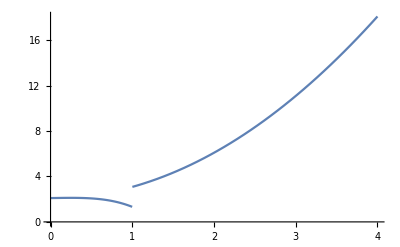

```mathematica
Plot[Re[Σreal[2.1,1.,z]],{z,0,4}]
```

```mathematica
FCircle[-2.1,-1.,E^(I Pi/4)]
```

0.495102-0.330295 ⅈ

```mathematica
ClearAll[ ΣAng];
ΣAng[p_,q_, M_] := 
Interpolation[
ParallelTable[
With[{ θ= 2  Pi n/M  },
{θ,Σ[p,q,E^(I θ)]}
],
{n,0,M}
],
PeriodicInterpolation->True];
```

```mathematica
ClearAll[Profile];
Profile[p_,q_] :=
Module[ { Σi  =ΣAng[p,q,4096]},
 PolarPlot[ Re[Σi[θ]],{θ,0, 2 Pi}]
];
```

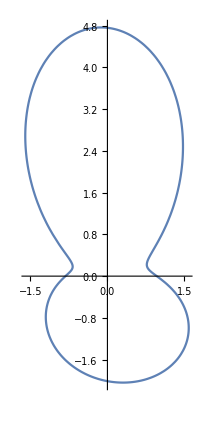

```mathematica
Profile[2.1,-1.]
```

```mathematica
h[Σi_,g_,θ_,ϵ_:10^(-8)]:=
g + I/(2 Pi) NIntegrate[
Module[
{Σ=Σi[θ+ α], Den},
Den = Exp[I α] -1;
Re[Σ]/Abs[Σ]Den/(Abs[Den]^2 + ϵ)]
,{α,0,2Pi} ,Method->"GaussKronrodRule"];
```

```mathematica
fprime[Σi_,η_,g_,c_,ϵ_:10^(-8)]:=
-c Conjugate[η]/(Pi (Abs[η]^2 + ϵ))NIntegrate[
Module[
{θ = Arg[η], r = Abs[η], Den, Σ},
Σ=Σi[θ+ α];
Den = r Exp[I α] -Re[Σ];
Abs[Σ]^2  h[Σi,g,θ+α,ϵ] Den/(Abs[Den]^2 + ϵ)]
,{α,0,2Pi} ,Method->"GaussKronrodRule"];

fn[Σi_,n_,g_,c_,ϵ_:10^(-8)]:= (* Laurent coefficient at η^(-n) *)
-c /Pi NIntegrate[
Module[
{Σ, ξ = E^(I θ)},
Σ=Σi[θ];
Abs[Σ]^2  h[Σi,g,θ,ϵ]] ξ^(n-1) Re[Σ]^(n-2)
,{θ,0,2Pi},Method->"GaussKronrodRule"];
```

```mathematica
LI =ListInterpolation[ Table[With[{z = r E^(I θ)},{{r,θ} ,  1/(1 + (3 + 2 I) z^2)}], {r,1,1.5,0.1},{θ,-Pi,Pi, Pi/10}]];
```

```mathematica
MakeOuterPointsAndBBox[Σi_,factor_,K_,M_,phase_]:=
Module[
{pts,scale, tbl, xbox, ybox,xy},
pts = Table[FromPolarCoordinates[{Re[Σi[θ]],θ}],{θ,-Pi + Pi/M+phase,Pi, Pi/M}];
scale = 1;
tbl = {};
Do[
tbl = Join[tbl,scale pts];
scale *= factor,
K];
xy = Transpose@( scale pts);
xbox = MinMax[xy[[1]]];
ybox = MinMax[xy[[2]]];
{tbl, xbox,ybox}
];
```

```mathematica
{ToPolarCoordinates[#],#[[1]] + I #[[2]]}& /@ {{1,2},{3,4}}
```

{{{√5,ArcTan[2]},1+2 ⅈ},{{5,ArcTan[4/3]},3+4 ⅈ}}

```mathematica
BoundaryData[Σi_,p_,q_,g_,c_,dr_,K_, M_] := 
Module[{Lint,data,factor =1.001},
Σi = ΣAng[p,q,1024];
data =ParallelTable[
 With[{z =r factor Re[Σi[θ]]E^(I θ)}, {{r ,θ},fprime[Σi,z,g,c, 10^(-8)]}],
{r,1,1+dr,dr/K}, {θ,-Pi +Pi/M, Pi,Pi/M}
];
data
];
```

```mathematica
SPOut[Σi_,p_,q_,g_,c_,dr_,K_, M_] :=
Module[{data,pts,xy,xbox,ybox},
data = BoundaryData[Σi,p,q,g,c,dr,K, M];
pts = FromPolarCoordinates[#[[1]]]& /@ data;
xy = Transpose@pts;
xbox = MinMax[xy[[1]]];
ybox = MinMax[xy[[2]]];
Lint = ListInterpolation[data,PeriodicInterpolation->{False,True}];
StreamPlot[
Module[{fp,a = (p + q), b = (p -q) },
{r,θ} = ToPolarCoordinates[{x,y}];
fp = Lint[r,θ];
{{x,y},{a x +Re[fp],b y + Im[fp]}}
],
{x,xbox[[1]],xbox[[2]]},{y,ybox[[1]],ybox[[2]]},
RegionFunction->Function[{x,y},Sqrt[x^2+ y^2] > Re[Σi[ ArcTan[x,y]]]],
StreamPoints->pts,
StreamScale->Tiny,
RegionFillingStyle->None,
AspectRatio->Automatic
]
];
```

```mathematica
MakeInnerPointsAndBBox[Σi_,factor_,M_,phase_]:=
Module[
{pts,scale, tbl, xbox, ybox,xy},
pts = Table[FromPolarCoordinates[{Re[Σi[θ]],θ}],{θ,-Pi + Pi/M+phase,Pi, Pi/M}];
xy = Transpose@pts;
xbox = MinMax[xy[[1]]];
ybox = MinMax[xy[[2]]];
scale = 1;
tbl = {};
While[Length[pts] > 1,
tbl = Join[tbl,scale pts];
pts = pts[[;;;;2]];
scale *= factor;
];
{tbl, xbox,ybox}
];
```

```mathematica
SPIn[Σi_,p_,q_, M_] :=
Module[{pts,xbox,ybox, factor = 0.9},
{pts, xbox,ybox}=MakeInnerPointsAndBBox[Σi,factor,M,0];
StreamPlot[
Module[{ a = (p + q), b = (p -q), c =1  },
{a x, b y}],
{x,xbox[[1]],xbox[[2]]},{y,ybox[[1]],ybox[[2]]},
RegionFunction->Function[{x,y},Sqrt[x^2+ y^2] < Re[Σi[ ArcTan[x,y]]]],
StreamPoints->pts,
StreamScale->Tiny,
RegionFillingStyle->None,
AspectRatio->Automatic
]
];
```

```mathematica
SPL[p_,q_,g_,c_,M_,drOut_,Kout_, Mout_] :=
Module[{Σi = ΣAng[p,q,1024]},
Show[{
SPIn[Σi,p,q,M],
SPOut[Σi,p,q,g,c,drOut,Kout, Mout]
}]
];
```

NIntegrate::inumr: The integrand ((-1+ⅇ^(ⅈ α)) Re[«1»[2 π+α+Arg[x+ⅈ y]]])/((1/100000000+Abs[-1+ⅇ^Times[«2»]]^2) Abs[InterpolatingFunction[«1»][2 π+α+Arg[x+Times[«2»]]]]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

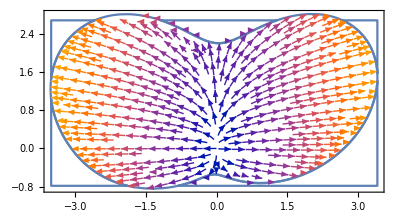

```mathematica
SPL[2.1,1.,5,1,1024,0.1,3,128]
```